Zad. 1

```mathematica
D[(x^4)^(1/3)-1/x,x]
D[x^3 Exp[Cos[x]],x]
```

1/x^2+(4 x^3)/(3 (x^4)^(2/3))

3 ⅇ^Cos[x] x^2-ⅇ^Cos[x] x^3 Sin[x]

Zad. 2

```mathematica
Integrate[x^2(1+x^3)^4,x]//FullSimplify
Integrate[Log[x],x]
```

1/15 x^3 (5+10 x^3+10 x^6+5 x^9+x^12)

-x+x Log[x]

Zad. 3

```mathematica
Series[Sqrt[x],{x,4,2}]//Normal
%/.{x->41/10}
%%/.{x->4.1}
Sqrt[4.1]
```

2+1/4 (-4+x)-1/64 (-4+x)^2

12959/6400

2.02484

2.02485

Zad. 4

```mathematica
(x-1)(4 x^2-1)//Expand;
Integrate[%,x]6//Expand
D[%,x]//Factor//TeXForm
```

6 x-3 x^2-8 x^3+6 x^4

6 (x-1) (2 x-1) (2 x+1)

Zad. 5           
f(x) = x^2, -1<=x<=2

```mathematica
f2[x_]:=x^2
f2[-1/2]+f2[1/2]+f2[3/2]
```

11/4

Zad. 6

2-3 x+x^2

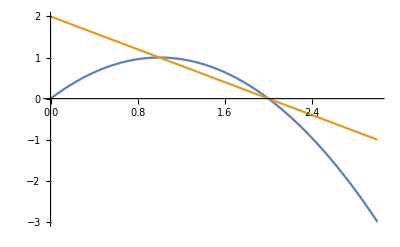

1/6

```mathematica
(x-1)(x-2)//Expand
y1=2x-x^2;
y2=2-x;
Plot[{y1,y2},{x,0,3}]
Integrate[y1-y2,{x,1,2}]
```

Zad. 7

```mathematica
Log[x y + 1];
D[%,y]
D[%,x]//Simplify
%//TeXForm
```

x/(1+x y)

1/(1+x y)^2

\frac{1}{(x y+1)^2}